## Compare matrix angles vs cpMONO angles for the balls in a superlattice Run common_funs, ES_FindSymGroups, BC_ChooseTmat Option A: BC_Cumulative, BC_Superlattice Option B: load a file saved by BC_Superlattice Superlattice has dimensions of (# discretized lattice points) x (# Σ for closest-to-Σ) (This is an expansion based on BC_CloseAlphaMONOsButFarTmats.nb)

```mathematica
Now
```

## User choices

```mathematica
Tmat=TmatBrownAn00;
```

#### load pre-saved file from BC_Superlattice

```mathematica
LoadFile=True;
```

#### If UseSamePtForComparison is True, then the pair of closest-toSigma maps will share the same lattice point. This means that the maps will be expected to be closer to each other the the case of UseSamePtForComparison = False, where the pair of closest-toSigma maps may or may not share the same lattice point.

```mathematica
UseSamePtForComparison=False;
```

#### node mode

```mathematica
nm=nm1
```

#### node sequence

```mathematica
Σn=ΣnTETXISO
```

#### number of maps to try

```mathematica
bMax=5;  (* start small *)
```

#### number of digits for displaying matrix entries

```mathematica
numdig=2;
```

#### optional: for plotting balls

```mathematica
Clear[options]
```

```mathematica
eye=50xyzTP[{30Degree,65Degree}];
```

```mathematica
eyeabove={0,0,20};
```

```mathematica
options[eye_]:={ViewPoint->eye,Lighting->{{"Ambient",White}},Boxed->False};
```

## Onwards

#### pre-saved file

```mathematica
mdir
idir=FileNameJoin[{mdir,"data"}]
itag=FileNameJoin[{idir,"BC_Superlattice_"<>Tlab[Tmat]}]
```

#### load file saved in BC_Superlattice.nb

```mathematica
If[LoadFile,Get[itag<>".m"]]
```

```mathematica
ListΣ
```

```mathematica
stAlpha1=Subscript[α, MONO]^T1;
stAlpha2=Subscript[α, MONO]^T2;
stDiff=Subscript[α, MONO]^T1 - Subscript[α, MONO]^T2;
stDiffNorm=(‖stDiff‖)_2
```

```mathematica
MatrixForm[Tmat]
```

#### number of balls in the superlattice

```mathematica
nlat=Length[RunPoints[nm,Σn,dt]]
nsig=Length[ListΣ]
nsup=nlat nsig
```

#### number of balls in the superlattice without ISO balls

```mathematica
(nlat-1)( nsig-1)
```

#### we will need to know the ISO point and TRIV point note: there’s probably a safer way to find these points, but it might require saving additional functions

```mathematica
PtISO={0.,4.5}; 
PtTRIV={0,0.5};
```

```mathematica
PtsSigs=PtsAndSigmas[nm,Σn,dt]
Length[PtsSigs]
```

#### cut the ISO lattice point from the discretized lattice and the closest-ISO points from ListΣ

```mathematica
IndexISO=MapIndexed[If[(#[[2]]===ISO||#[[1]]===PtISO),First[#2],Nothing]&,PtsSigs]
PtsSigs[[IndexISO]]
```

#### cut ISO points from PtsSigs and from AllClosests

```mathematica
PtsSigsNoISO=Delete[PtsSigs,List/@IndexISO];
Length[PtsSigsNoISO]
```

```mathematica
AllMaps=AllClosests[Tmat,dt,Σn,nm];
Length[AllMaps]
```

```mathematica
AllMapsNoISO=Delete[AllMaps,List/@IndexISO];
Length[AllMapsNoISO]
```

```mathematica
PtsNOISO=First/@PtsSigsNoISO
Length[PtsNOISO]
```

```mathematica
(*Take[PtsSigsNoISO,10]
Take[PtsSigsNoISO,-10]*)
```

#### showing the lattice requires LatticeWithPts from Cumulative

```mathematica
(* LatticeWithPts[dt,{}]
LatticeWithPts[dt,Σn] *)
```

#### key functions for numerical integration on the sphere

```mathematica
NAverageOverSphere[f_]:=√(1/(4 π)NIntegrate[f[{θ,ϕ}]^2 Sin[ϕ],{θ,0,2π},{ϕ,0,π}]);
```

```mathematica
pg=3;ag=3;
```

```mathematica
L2norm[f_]:=Sqrt[1/(4 π) NIntegrate[f[{θ,ϕ}]^2 Sin[ϕ],{θ,0,2 π},{ϕ,0,π},AccuracyGoal->ag,PrecisionGoal->pg]];
```

```mathematica
L2normOfAlphaDiffs[{Tmat1_,Tmat2_}]:=L2norm[1.(Alpha[Tmat1,#,MONO]-Alpha[Tmat2,#,MONO])/Degree &];
```

#### random map in the discretized lattice

```mathematica
Ttest=RandomChoice[AllMapsNoISO];
MatrixForm[Ttest]
DispMat[Ttest,numdig]
```

#### ElasticMapPairsPrelim are the pairs of AllClosests Option A: any two maps in the superlattice

```mathematica
Clear[ElasticMapPairsPrelim,ElasticMapPairs]
```

```mathematica
ElasticMapPairsPrelim[Tmat_,dt_,Σn_,nm_]:=CartesianProduct[{AllMapsNoISO,AllMapsNoISO}];
ElasticMapPairs[Tmat_,dt_,Σn_,nm_]=Select[ElasticMapPairsPrelim[Tmat,dt,Σn,nm],#[[1]]!=#[[2]]&];
Length[ElasticMapPairsPrelim]
Length[ElasticMapPairs]
```

#### an example pair of maps

```mathematica
Row[DispMat[#,numdig]&/@RandomChoice[ElasticMapPairs[Tmat,dt,Σn,nm]]]
```

#### Option B: two maps having the same lattice point note: probably the input argument should be changed from PtsNOISO to nm, Σn, dt

```mathematica
Clear[TwoMatSamePt]
```

```mathematica
TwoMatSamePt[PtsNOISO_]:=Module[{ptx,iptx},
ptx=RandomChoice[PtsNOISO];
iptx=Flatten[Position[PtsNOISO,ptx]];
If[Length[iptx]>=2,AllMapsNoISO[[RandomChoice[iptx,2]]],{}]];
```

#### an example pair of maps

```mathematica
Row[DispMat[#,numdig]&/@TwoMatSamePt[PtsNOISO]]
```

#### KEY CALCULATION note: after a few warning messages, it will show this: “General: Further output of NIntegrate::slwcon will be suppressed during this calculation” and then stop displaying messages

```mathematica
(* TableOf4tuples={#[[1]],#[[2]],L2normOfAlphaDiffs[#],AngleMatrix[#[[1]],#[[2]]]/Degree}&/@RandomChoice[ElasticMapPairs[Tmat,dt,Σn,nm],bMax]; *)
```

```mathematica
nbetweentext=1;
TableOf4tuples=Table[With[
{choice=If[UseSamePtForComparison,TwoMatSamePt[PtsNOISO],RandomChoice[ElasticMapPairs[Tmat,dt,Σn,nm]]]},
With[{startTime=AbsoluteTime[]},
avgDiff=L2normOfAlphaDiffs[choice];
duration=AbsoluteTime[]-startTime;
If[Mod[i,nbetweentext]==0,Print["Evaluation ",i,", Duration: ",NumberForm[duration,{Infinity,2}]," seconds"]];
{choice[[1]],choice[[2]],avgDiff,AngleMatrix[choice[[1]],choice[[2]]]/Degree,duration}]],{i,bMax}];
```

#### test of TableOf4tuples (note the use of Chop and MakeReal)

```mathematica
(* {MatrixForm[Round[#[[1]],.01]],MatrixForm[Round[#[[2]],.01]],#[[3]],#[[4]]}&/@Take[TableOf4tuples,2] *)
```

```mathematica
nshow = 4;
{DispMat[#[[1]],numdig],DispMat[#[[2]],numdig],Chop[#[[3]],0.001],Chop[MakeReal[#[[4]]],0.001]}&/@Take[TableOf4tuples,nshow]
```

#### plot

```mathematica
(* Graphics[Point[MakeReal[points]]] *)
```

```mathematica
If[UseSamePtForComparison,slope1=2.8,slope1=1.5];
slope2=6;
```

```mathematica
xypoints=MakeReal[{#[[3]],#[[4]]}&/@Take[TableOf4tuples,All]];
xMin=Min[xypoints[[All,1]]];
xMax=Max[xypoints[[All,1]]];
yMin=Min[0,Min[xypoints[[All,2]]]];
yMax=Max[0,Max[xypoints[[All,2]]]];
xMin=0;yMin=0;

xyplotWithoutPoints=Graphics[{{Dashed,Line[{{xMin,slope1*xMin},{xMax,slope1*xMax}}]},{Dashed,Line[{{xMin,slope2*xMin},{xMax,slope2*xMax}}]}},AxesOrigin->{0,0},Frame->True,
FrameLabel->{Style[stDiffNorm,24],Style[Row[{Style["∠",32],Style["(T1, T2)",20]}]]},
AspectRatio->1,FrameTicksStyle->14,ImageSize->500,PlotRange->{{xMin,xMax},{yMin,1.05yMax}}]

fontsize=14; 
snums=SequenceForm[nsup," = ",nlat," x ",nsig," elastic maps"];
snm=SequenceForm["node mode is ",TextNM[nm]];
sdt=SequenceForm["dt = ",dt];
sns=SequenceForm["node sequence is ",Σn];
sbmx=SequenceForm[bMax," random (T1,T2) pairs"];
stbox=SequenceForm[MatrixNote[Tmat],"\n\n",snm,"\n\n",sdt,"\n\n",snums,"\n\n",sbmx];
If[nm===nm3,stbox=SequenceForm[stbox,"\n\n",sns]];
If[UseSamePtForComparison,stbox=SequenceForm[stbox,"\n\n T1 and T2 share same lattice pt"]];
xyplot=Show[xyplotWithoutPoints,Graphics[{PointSize[.01],Point[xypoints]}],Epilog->{Inset[Framed[Style[stbox,fontsize,LineSpacing->{0.7,0}],FrameMargins->Medium,FrameStyle->Black],Scaled[{0.97,0.03}],{Right,Bottom}]}]
```

## Plot elastic maps as rectangles

#### contours for balls

```mathematica
Clear[contours,MaxForScaling];
MaxForScaling=17;
cmax=MaxForScaling+1;
contours=Range[0,cmax,1];
```

```mathematica
MaxForScalingDiff=12;
cmax=MaxForScalingDiff+1;
contoursDiff=Range[-cmax,cmax,1];
```

#### two example maps (change itry)

```mathematica
itry=1;
Tmat1=TableOf4tuples[[itry]][[1]];
Tmat2=TableOf4tuples[[itry]][[2]];
DispMat[Tmat1,numdig]
DispMat[Tmat2,numdig]
```

#### maps with automatic contours

```mathematica
(* ContourPlot[Alpha[Tmat1,{θ,ϕ},MONO]/Degree,{θ,0,2π},{ϕ,0,π},PlotRange->All,AspectRatio->Automatic,ColorFunction->(ColorData["TemperatureMap"]),FrameTicks->{Range[0,2π,π/4],Range[0,2π,π/4]},ImageSize->600]

ContourPlot[Alpha[Tmat2,{θ,ϕ},MONO]/Degree,{θ,0,2π},{ϕ,0,π},PlotRange->All,AspectRatio->Automatic,ColorFunction->(ColorData["TemperatureMap"]),FrameTicks->{Range[0,2π,π/4],Range[0,2π,π/4]},ImageSize->600]

ContourPlot[Alpha[Tmat1,{θ,ϕ},MONO]/Degree-Alpha[Tmat2,{θ,ϕ},MONO]/Degree,{θ,0,2π},{ϕ,0,π},PlotRange->All,AspectRatio->Automatic,ColorFunction->(ColorData["TemperatureMap"]),FrameTicks->{Range[0,2π,π/4],Range[0,2π,π/4]},ImageSize->600] *)
```

#### map with user-specified contours note: the min/max of the color legend will vary based on the contours plotted, but each contour should have the same color in each plot

```mathematica
(* Show[cpMONOprelim[Tmat1,contours,Automatic,MaxForScaling,plotpoints,contourstyle],FrameTicks->{Range[0,2π,π/4],Range[0,2π,π/4]},ImageSize->600]
Show[cpMONOprelim[Tmat2,contours,Automatic,MaxForScaling,plotpoints,contourstyle],FrameTicks->{Range[0,2π,π/4],Range[0,2π,π/4]},ImageSize->600] *)
```

#### ColorData["TemperatureMap"] is a function that takes numbers and gives you colors. The range from 0 to 1 gets all of the temperature colors.

```mathematica
ColorData["TemperatureMap"][.8]
ColorData["TemperatureMap"]/@Range[0,1,.1]
```

#### difference between two Alpha functions ColorFunctionScaling -> False is crucial. Otherwise Mathematica scales things to give the entire range from blue to red .

```mathematica
Clear[cpPrelimForDIFF];
cpPrelimForDIFF[Tmat1_,Tmat2_,contours_,legends_,MaxForScalingDiff_]:=cpPrelimForDIFF[Tmat1,Tmat2,contours,legends,MaxForScalingDiff]=ContourPlot[Alpha[Tmat1,{θ,ϕ},MONO]/Degree-Alpha[Tmat2,{θ,ϕ},MONO]/Degree,
{θ,0,2π},{ϕ,0,π},Contours->contours,ContourStyle->Thickness[.003],ColorFunction->(ColorData["TemperatureMap"][(#+MaxForScalingDiff)/(2MaxForScalingDiff)]&),ColorFunctionScaling->False,PlotLegends->legends,PlotRange->All,AspectRatio->Automatic];
```

#### Try this, after you have decided on contours and MaxForScalingDiff.

```mathematica
MaxForScalingDiff
contoursDiff
```

```mathematica
(* Show[cpPrelimForDIFF[Tmat1,Tmat2,contoursDiff,Automatic,MaxForScalingDiff],FrameTicks->{Range[0,2π,π/4],Range[0,2π,π/4]},ImageSize->600] *)
```

## Plot elastic maps as balls

#### optional: plot principal axes (use {} to NOT plot)

```mathematica
PaxesForLattice=Paxes[True,True,True,id,{0,0,0},1.35,1,.17,.009,"TriColor",ArrowColor];
```

```mathematica
PaxesForLattice={};
```

#### Plot on sphere with center and radius.

```mathematica
If[$VersionNumber<12,
cpDIFF[center_,BBrad_,Tmat1_,Tmat2_,contours_,MaxForScalingDiff_]:=
Graphics3D[GraphicsComplex[center+BBrad×xyzTP[#]&/@cpPrelimForDIFF[Tmat1,Tmat2,contours,None,MaxForScalingDiff][[1,1]], 
                                                                                                                        cpPrelimForDIFF[Tmat1,Tmat2,contours,None,MaxForScalingDiff][[1,2]]]],
cpDIFF[center_,BBrad_,Tmat1_,Tmat2_,contours_,MaxForScalingDiff_]:=
Graphics3D[GraphicsComplex[center+BBrad×xyzTP[#]&/@cpPrelimForDIFF[Tmat1,Tmat2,contours,None,MaxForScalingDiff][[1,1,1]], 
                                                                                                                        cpPrelimForDIFF[Tmat1,Tmat2,contours,None,MaxForScalingDiff][[1,1,2]]]]];
```

#### Plot on sphere.

```mathematica
cpDIFF[Tmat1_,Tmat2_,contours_,MaxForScalingDiff_]:=cpDIFF[{0,0,0},1,Tmat1,Tmat2,contours,MaxForScalingDiff];
```

```mathematica
(* cpDIFF[Tmat1,Tmat2,contoursDiff,MaxForScalingDiff]*)
```

#### given a point (x0,y0), return the index of the closest (x,y) in points

```mathematica
GetIndex[xypoints_,x0_,y0_]:=Module[{nearestFunction,nearestPointIndex,nearestPoint},nearestFunction=Nearest[xypoints->"Index"];
nearestPointIndex=nearestFunction[{x0,y0}][[1]];
nearestPoint=xypoints[[nearestPointIndex]];
Print["Pair ",nearestPointIndex," gives ",nearestPoint," as the closest to (",x0,", ",y0,")"];
nearestPointIndex]
```

```mathematica
itry=GetIndex[xypoints,2,20];
xypoints[[itry]]
```

#### given (x0,0), find the closest (x,y) and display the two balls associated with the pair

```mathematica
Clear[ShowBallsTmat]
```

```mathematica
ShowBallsTmat[Tmat1_,Tmat2_,eye_]:=Module[{},
Print[Row[{Style["T_1 = ",18],Style[DispMat[Tmat1,2],14],Style["   T_2 = ",18],Style[DispMat[Tmat2,2],14]}]];
Print[Style["dMONO = ",16],Style[Round[L2normOfAlphaDiffs[{Tmat1,Tmat2}],0.01],16],Style[" and ",16],Style[∠,20],Style["(T_1,T_2) = ",16],Style[N[AngleMatrix[Tmat1,Tmat2]/Degree],16]];
GraphicsRow[{Labeled[Show[{cpMONO[Tmat1,contours,MaxForScaling,plotpoints,contourstyle],Graphics3D[PaxesForLattice]},options[eye]],Style[Text[stAlpha1],16],Bottom,FrameMargins->0],Labeled[Show[{cpMONO[Tmat2,contours,MaxForScaling,plotpoints,contourstyle],Graphics3D[PaxesForLattice]},options[eye]],Style[Text[stAlpha2],16],Bottom,FrameMargins->0],Labeled[Show[{cpDIFF[Tmat1,Tmat2,contoursDiff,MaxForScalingDiff],Graphics3D[PaxesForLattice]},options[eye]],Style[Text[stDiff],28],Bottom,FrameMargins->0]},Spacings->0,ImageSize->600]]
```

```mathematica
(* ShowBallsTmat[Tmat1,Tmat2,eye] *)
```

```mathematica
Clear[ShowBalls]
```

```mathematica
ShowBalls[x0_,y0_,eye_]:=Module[{itry,Tmat1,Tmat2,dMONO,beta,graphics},
itry=GetIndex[xypoints,x0,y0];
Tmat1=TableOf4tuples[[itry]][[1]];
Tmat2=TableOf4tuples[[itry]][[2]];
dMONO=MakeReal[TableOf4tuples[[itry]][[3]]];
beta=MakeReal[TableOf4tuples[[itry]][[4]]];
Print[Row[{Style["T_1 = ",18],Style[DispMat[Tmat1,2],14],Style["   T_2 = ",18],Style[DispMat[Tmat2,2],14]}]];
Print[Style["dMONO = ",16],Style[Round[dMONO,0.01],16],Style[" and ",16],Style[∠,20],Style["(T_1,T_2) = ",16],Style[beta,16]];
GraphicsRow[{Show[cpMONO[Tmat1,contours,MaxForScaling, plotpoints,contourstyle],options[eye]],
Show[cpMONO[Tmat2,contours,MaxForScaling, plotpoints,contourstyle],options[eye]],
Show[cpMONO[Tmat1,Tmat2,contoursDiff,MaxForScalingDiff, plotpoints,contourstyle],options[eye]],
Show[xyplotWithoutPoints,Epilog->{Red,PointSize[0.05],Point[{dMONO,beta}]},ImageSize->400]},Spacings->20,ImageSize->900]
]
```

#### examples

```mathematica
(* ShowBalls[7,20,eye]
ShowBalls[5,15,eye]
ShowBalls[3.5,10,eye]
ShowBalls[2,12,eye]
ShowBalls[1.8,5,eye]
ShowBalls[1.5,8,eye]
ShowBalls[0.8,5,eye]
ShowBalls[1,1,eye] *)
```

## Examples (adjust PaxesForLattice above)

#### Exceptional example (see BC_CloseAlphaMONOsButFarTmats.nb)

```mathematica
(*Clear[contours,MaxForScaling]
dc=1; MaxForScaling=18; cmax=MaxForScaling+dc; contours=Range[0,cmax,dc];
Clear[contoursDiff,MaxForScalingDiff]
dc=0.2;MaxForScalingDiff=0.6;cmax=MaxForScalingDiff+dc;contoursDiff=Range[-cmax,cmax,dc];
*)
```

```mathematica
Tmat1=({{8, 0, 0, 0, 0, 0}, {0, 8, 0, 0, 0, 0}, {0, 0, 5, 0, 0, 0}, {0, 0, 0, 15, 0, 0}, {0, 0, 0, 0, 7, 0}, {0, 0, 0, 0, 0, 10}});Tmat2=({{8, 0, 0, 0, 0, 0}, {0, 8, 0, 0, 0, 0}, {0, 0, 15, 0, 0, 0}, {0, 0, 0, 5, 0, 0}, {0, 0, 0, 0, 7, 0}, {0, 0, 0, 0, 0, 10}});
```

```mathematica
Tmat2==MatrixUbar[ZRot[π/4]].Tmat1.Transpose[MatrixUbar[ZRot[π/4]]]
```

```mathematica
(*ShowBallsTmat[Tmat1,Tmat2,eye]
ShowBallsTmat[Tmat1,Tmat2,eyeabove]*)
```

#### Compare TRIV with closest-MONO

```mathematica
(* Tmat1=Tmat;
Tmat2=Closest[Tmat,MONO];*)
```

```mathematica
(*Clear[contours,MaxForScaling]
dc=2;  MaxForScaling=24;  cmax=MaxForScaling+dc; contours=Range[0,cmax,dc];
Clear[contoursDiff,MaxForScalingDiff]
dc=0.25;MaxForScalingDiff=2;cmax=MaxForScalingDiff+dc;contoursDiff=Range[-cmax,cmax,dc];
*)
```

```mathematica
(*MatrixNote[Tmat]
ShowBallsTmat[Tmat1,Tmat2,eye]
ShowBallsTmat[Tmat1,Tmat2,eyeabove]*)
```

#### Testing: plot one map from two perspectives 1. hover mouse over contours to see their values 2. double-click to rotate balls

```mathematica
(*Tmat1=Closest[Tmat,XISO];*)
```

```mathematica
(*Clear[contours,MaxForScaling]
dc=1;  MaxForScaling=18;  cmax=MaxForScaling+dc; contours=Range[0,cmax,dc];*)
```

```mathematica
(*GraphicsRow[{Show[{cpMONO[Tmat1,contours,MaxForScaling,plotpoints,contourstyle],Graphics3D[PaxesForLattice]},options[eye]],Show[{cpMONO[Tmat1,contours,MaxForScaling,plotpoints,contourstyle],Graphics3D[PaxesForLattice]},options[eyeabove]]},Spacings->0,ImageSize->800]*)
```

## BrownAn00

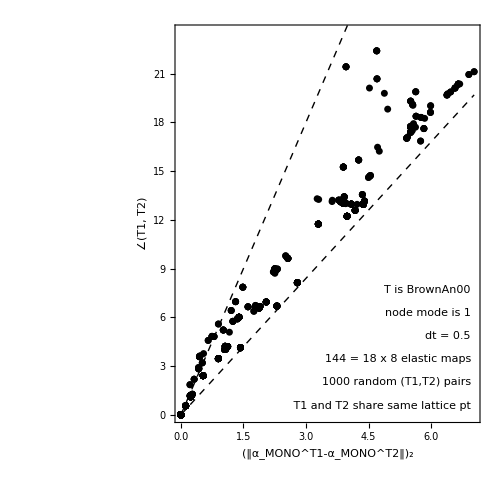

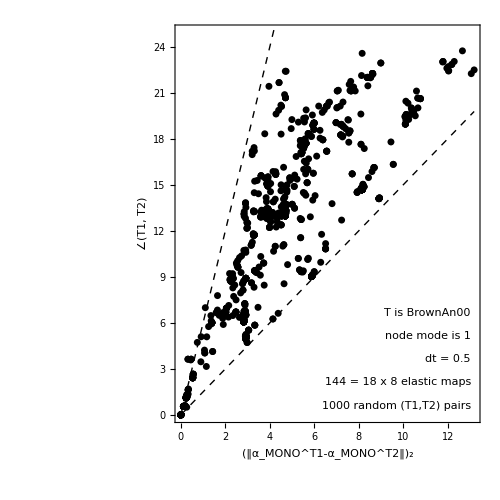

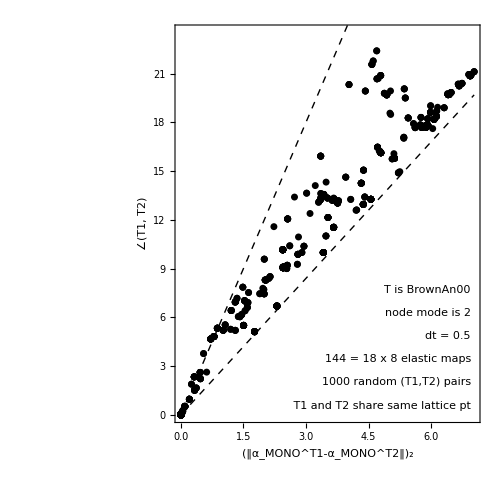

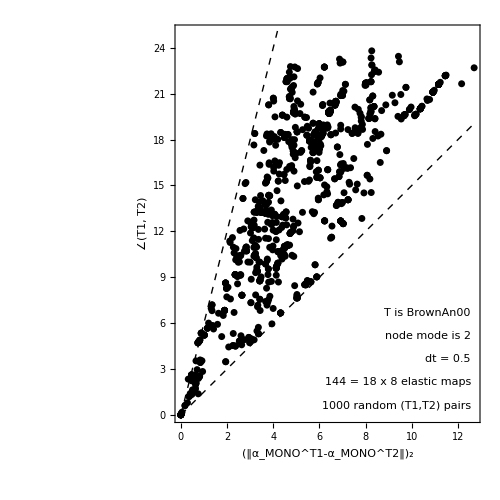

## BrownAn96

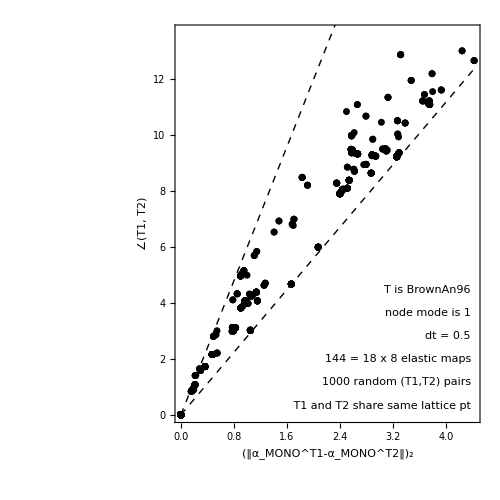

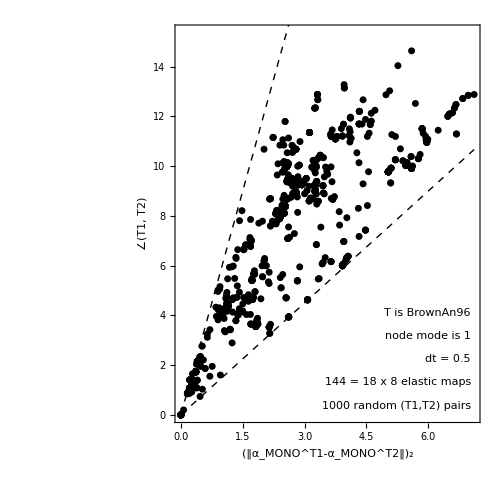

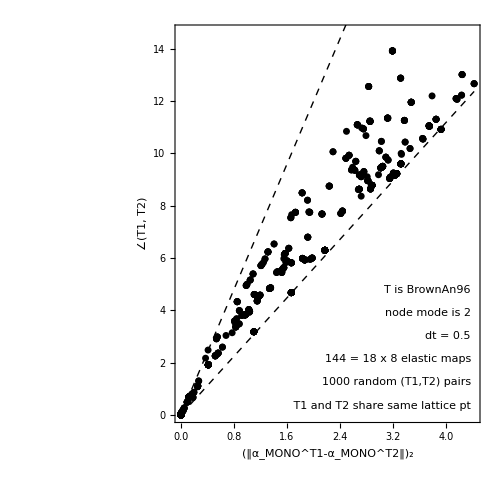

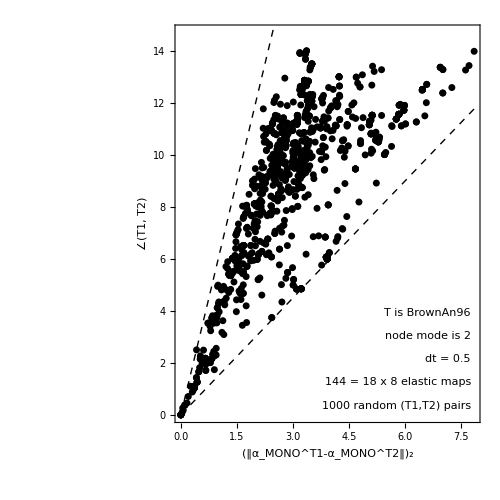

## Igel

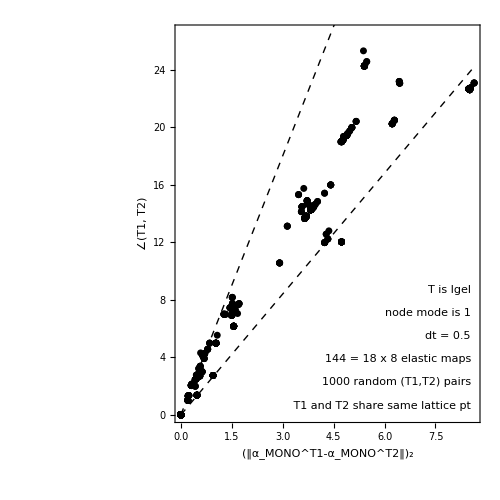

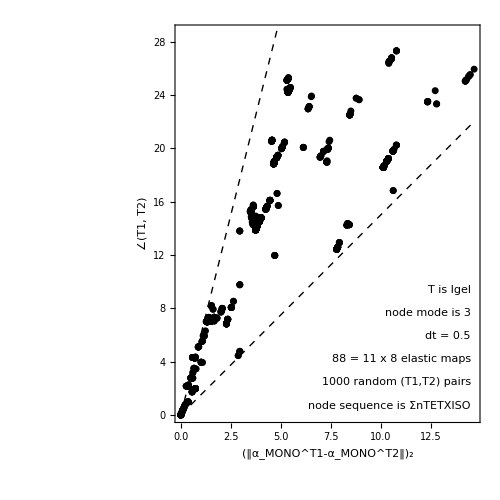

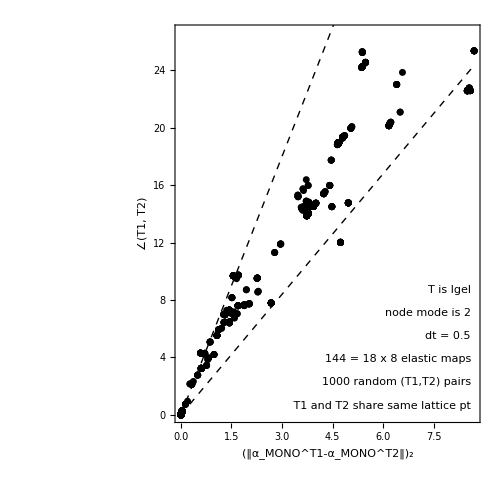

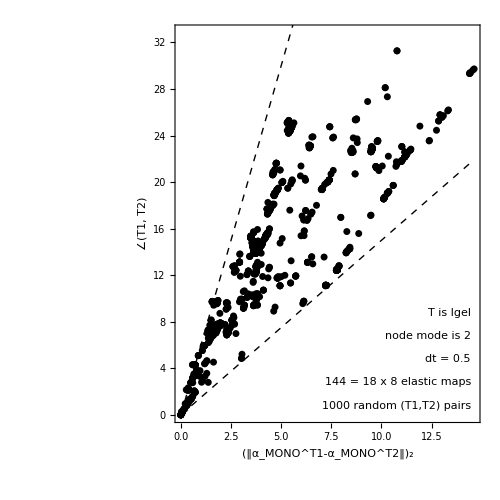

## SSA2023